## Graph of R package dependencies

## Importing data

```mathematica
json=Import["/Users/blmayer/doctorate/visualizacao/exercises/packages.json"];
```

## Transform

```mathematica
packages=#[[1]]->#[[2]]&@*Values/@json[[All,{1,2}]]
```

{A3→xtable,A3→pbapply,abc→abc.data,abc→quantreg,abc→locfit,abcdeFBA→Rglpk,abcdeFBA→rgl,abcdeFBA→corrplot,abctools→abc,abctools→abind,abctools→plyr,abctools→Hmisc,abd→mosaic,48178,weibulltools→RcppArmadillo,wicket→BH,womblR→RcppArmadillo,wv→RcppArmadillo,xdcclarge→RcppArmadillo,xslt→Rcpp,YPPE→BH,YPPE→RcppEigen,YPPE→StanHeaders,yuima→RcppArmadillo,zic→RcppArmadillo,ziphsmm→RcppArmadillo,ZVCV→RcppArmadillo}
 |  |  |  |

## Filter

```mathematica
communities=FindGraphCommunities[packages];
```

```mathematica
community=Select[packages, Length[Intersection[#/.Rule->List,communities[[1]]]]>0&];
```

## See

```mathematica
communities=FindGraphCommunities[packages];
```

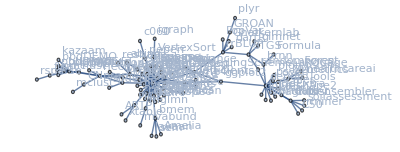

```mathematica
n=12;
g=Graph[Select[packages, Length[Intersection[#/.Rule->List,communities[[n]]]]>0&], VertexLabels->"Name",DirectedEdges->False]
```

## Exporting

```mathematica
hexString[color_]:=
"#"<>StringJoin[
StringPadLeft[IntegerString[IntegerPart[255color[[1]]],16],2,"0"],
StringPadLeft[IntegerString[IntegerPart[255color[[2]]],16],2,"0"],
StringPadLeft[IntegerString[IntegerPart[255color[[3]]],16],2,"0"]
]
```

```mathematica
Export[NotebookDirectory[]<>"matrix-"<>ToString[n]<>".json", AdjacencyMatrix[g]//Normal]
```

/Users/blmayer/doctorate/visualizacao/exercises/matrix-12.json

```mathematica
Export[NotebookDirectory[]<>"packages-"<>ToString[n]<>".csv",Join[{{"name", "color"}}, {#,hexString[RandomColor[]]}&/@VertexList[g]]]
```

/Users/blmayer/doctorate/visualizacao/exercises/packages-12.csv